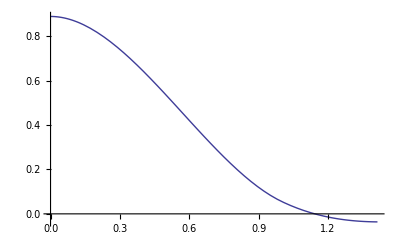

```mathematica
(* Mitchell-Netravali *)
b = 1/3; c = 1/3; (* subjective best values *)
P1[x_] := ((6-2 b) + (-18+12 b+6c) x^2  +(12-9b-6c) x^3)/6
P[x_] := ((8b+24c) + (-12b-48c)x +(6b+30c)x^2 +(-b-6c)x^3)/6
filtMN[x_] := If[x ≤ 1, P1[x], If[x ≤ √2, P[x],0]]
Plot[filtMN[x], {x, 0, √2}]
transMN[r_] := 2 NIntegrate[filtMN[Norm[{r,x}]], {x, 0, √2}]
```

```mathematica
steps = 100.0;
xAtStep[i_] := i √2 / steps
supportMN = Table[0, {i,steps+1}, {j,2}];
For[i=0, i <= steps, i += 1, supportMN[[i+1]] = {xAtStep[i], transMN[xAtStep[i]]}]
supportMN;
interpMN = Fit[supportMN, {1,x,x^2,x^3}, x]
Integrate[interpMN, {x, 0, √2}]
(* ListPlot[supportMN] *)
```

1.05671-0.402299 x-1.65744 x^2+1.01315 x^3

0.542622

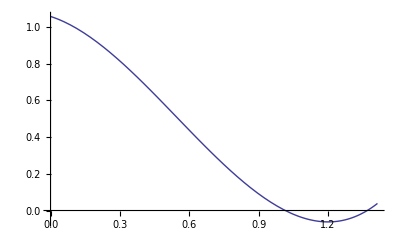

```mathematica
Plot[interpMN, {x, 0, √2}]
```